```mathematica
pauliMatrix[0]={{1,0},{0,1}};
pauliMatrix[1]={{0,1},{1,0}};
pauliMatrix[2]={{0,-ⅈ},{ⅈ,0}};
pauliMatrix[3]={{1,0},{0,-1}};

(*Definition of the matrices ψ*)
DiracMatrix[i_Integer?Positive,Dimension->n_Integer?Positive]/;If[OddQ[n],n=!=i,True]:=Module[{ν=n/2},Which[i==1,KroneckerProduct@@Table[pauliMatrix[1],{ν}],

2 ν>i>1&&EvenQ[i],
KroneckerProduct[Sequence@@Table[pauliMatrix[1],{ν-i/2}],pauliMatrix[2],Sequence@@Table[pauliMatrix[0],{i/2-1}]],2 ν>i>1&&OddQ[i],KroneckerProduct[Sequence@@Table[pauliMatrix[1],{ν-(i-1)/2}],pauliMatrix[3],Sequence@@Table[pauliMatrix[0],{(i-1)/2-1}]],
i==2 ν,KroneckerProduct[pauliMatrix[2],Sequence@@Table[pauliMatrix[0],{ν-1}]]]]

DiracMatrix[i_Integer?Positive,Dimension->n_Integer?Positive]/;n==i&&OddQ[i]:=Module[{ν=(n-1)/2},(-I)^ν Dot@@Table[DiracMatrix[j,Dimension->n],{j,2ν}]]
```

```mathematica
n=16; (*The number of fermions in our system*)
s=(3!)/n^3 J^2;
J=1;
dist= 1/(√(2π s))ⅇ^(-x^2/(2s)); 
gauss=ProbabilityDistribution[dist,{x,-Infinity, Infinity}];
random := RandomVariate[gauss];
```

```mathematica
(*Generating the random coupling tensor Subscript[J, abcd]*)
tensorJ = Normal@ SymmetrizedArray[_ :> random, {n,n,n,n},Antisymmetric[All]];
(*Generates an array containing all Subscript[ψ, i] from i=1 to n*)
psi= Table[DiracMatrix[i,Dimension-> n],{i,n}];
```

```mathematica
(*Definition of the Hamiltonian*)
H=Sum[If[a<b <c<d, tensorJ[[a,b,c,d]]*psi[[a]].psi[[b]].psi[[c]].psi[[d]],0],{a,n},{b,n},{c,n},{d,n}];
```

$Aborted

```mathematica
evalH = Eigenvalues[H];
diagH = DiagonalMatrix[evalH];
```

```mathematica
Zt = Sum[ⅇ^(-(β+I*t)evalH[[i]]),{i,2^Floor[n/2]}];
Z= Sum[ⅇ^(-β*evalH[[i]]),{i,2^Floor[n/2]}];
```

```mathematica
avgZts = Integrate[dist*Zt*Conjugate[Zt],{x,-Infinity,+Infinity}]/Integrate[dist,{x,-Infinity,+Infinity}];
avgZ= Integrate[dist*Z,{x,-Infinity,+Infinity}]/Integrate[dist,{x,-Infinity,+Infinity}];
```

```mathematica
gt=avgZts/(avgZ)^2;
β=5;
```

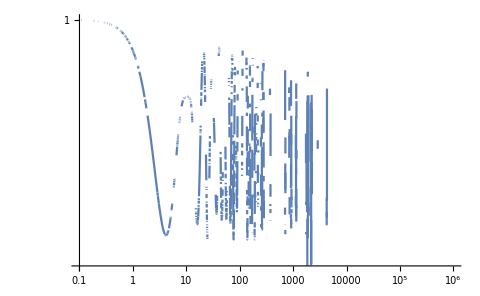

```mathematica
LogLogPlot[gt,{t,0.1,10^6},PlotPoints->100]
```